```mathematica
k15=Import["/home/matt/git/source/verdant-octo-kumquat/report/cache_out_15000.txt", "Table"];
k20=Import["/home/matt/git/source/verdant-octo-kumquat/report/cache_out_20000.txt", "Table"];
k25=Import["/home/matt/git/source/verdant-octo-kumquat/report/cache_out_25000.txt", "Table"];
```

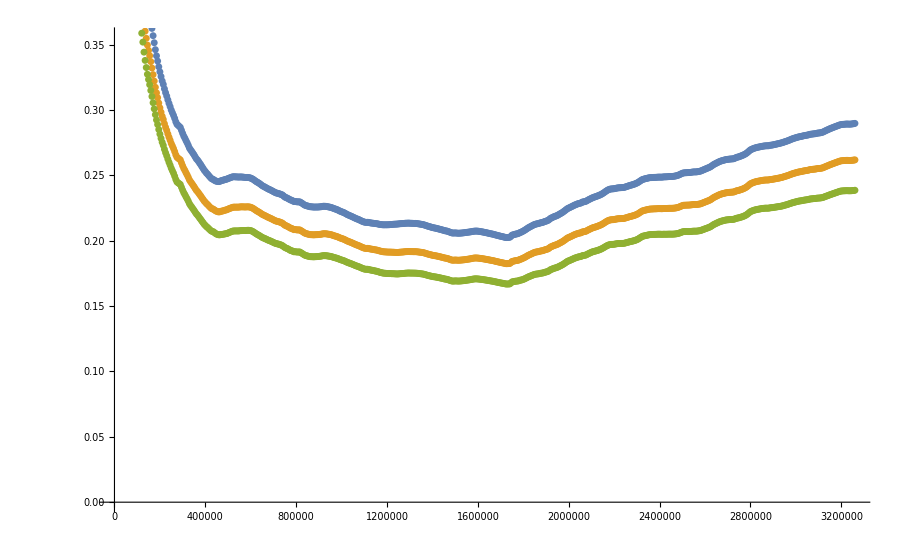

```mathematica
ListPlot[{k15,k20,k25}]
```

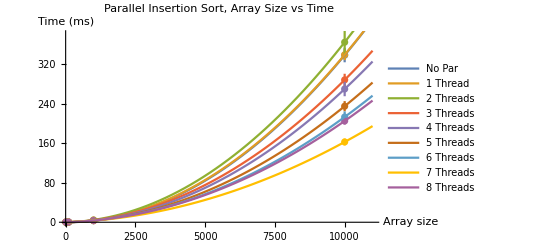

```mathematica
Err=ErrorListPlot[{DS0,DS1,DS2,DS3,DS4,DS5,DS6,DS7,DS8}];
BF = Plot[{M0[x],M1[x],M2[x],M3[x],M4[x],M5[x],M6[x],M7[x],M8[x]},{x,0,11000}, PlotLegends->{"No Par","1 Thread","2 Threads" , "3 Threads", "4 Threads", "5 Threads", "6 Threads", "7 Threads", "8 Threads"}];
Show[Err,BF,AxesLabel-> {"Array size", "Time (ms)"},PlotRange->{{0,11000},{0,380}}, PlotLabel-> "Parallel Insertion Sort, Array Size vs Time"]
```

```mathematica
Coeffs={{1,M0''[x]/2}, {2,M1''[x]/2},{3, M2''[x]/2}, {4,M3''[x]/2}, {5,M4''[x]/2}, {6,M5''[x]/2}, {7,M6''[x]/2}, {8,M7''[x]/2}}
```

{{1,3.39839×10^-6},{2,3.36342×10^-6},{3,3.52624×10^-6},{4,2.74726×10^-6},{5,2.60706×10^-6},{6,2.22467×10^-6},{7,1.98918×10^-6},{8,1.44375×10^-6}}

```mathematica
Lm=LinearModelFit[Coeffs,x,x]
```

FittedModel[3.98028×10^-6-2.9284×10^-7 x]

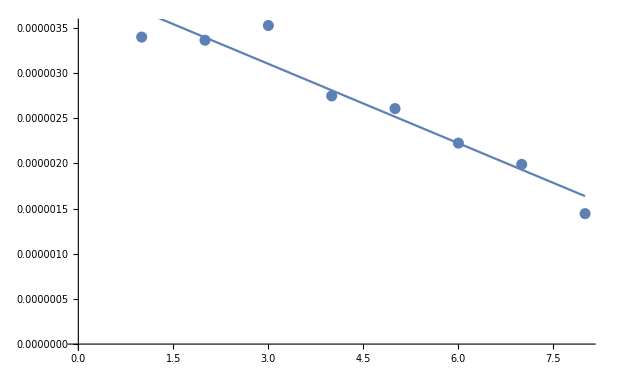

```mathematica
Show[{ListPlot[Coeffs],Plot[Lm[x],{x,1,8}]}]
```

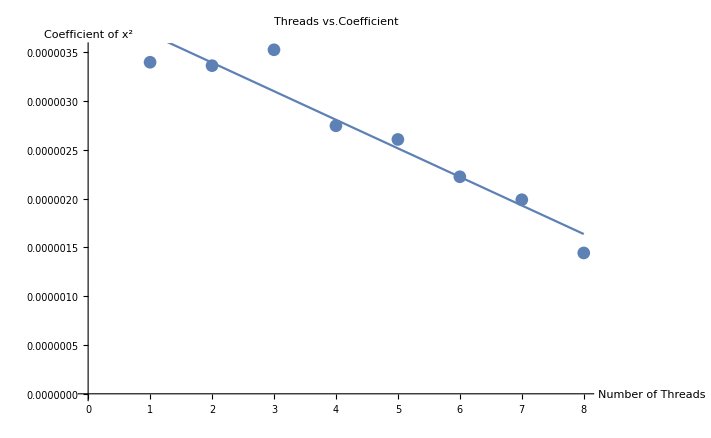

```mathematica
Show[%50,AxesLabel->{HoldForm[Number of Threads],HoldForm[Coefficient of x^2]},PlotLabel->HoldForm[Threads vs.Coefficient],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Lm["RSquared"]
```

0.918917